# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-01

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Brazil,Canada,Chile,Denmark,France,Germany,India,Ireland,Israel,Netherlands,Norway,Portugal,Singapore,South Africa,Spain,Sweden,Switzerland,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Brazil,Canada,Chile,Denmark,France,Germany,India,Ireland,Israel,Netherlands,Norway,Portugal,Singapore,South Africa,Spain,Sweden,Switzerland,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2021-12-18,197},{2021-12-19,129},{2021-12-20,142},{2021-12-21,434},{2021-12-22,467},{2021-12-23,414},{2021-12-24,327},{2021-12-25,218},{2021-12-26,197},{2021-12-27,110},{2021-12-28,167},{2021-12-29,74},{2021-12-30,102},{2021-12-31,17},{2022-01-01,9}},Brazil→{{2021-12-18,15},{2021-12-19,9},{2021-12-20,43},{2021-12-21,63},{2021-12-22,54},{2021-12-23,48},{2021-12-24,6},{2021-12-25,8},{2021-12-26,12},{2021-12-27,32},{2021-12-28,35},{2021-12-29,5},{2021-12-30,1},{2021-12-31,0},{2022-01-01,0}},Canada→{{2021-12-18,198},{2021-12-19,172},{2021-12-20,391},{2021-12-21,58},{2021-12-22,0},{2021-12-23,1},{2021-12-24,0},{2021-12-25,0},{2021-12-26,3},{2021-12-27,68},{2021-12-28,8},{2021-12-29,0},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Chile→{{2021-12-18,69},{2021-12-19,49},{2021-12-20,59},{2021-12-21,25},{2021-12-22,8},{2021-12-23,6},{2021-12-24,4},{2021-12-25,0},{2021-12-26,0},{2021-12-27,1},{2021-12-28,10},{2021-12-29,0},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Denmark→{{2021-12-18,940},{2021-12-19,1204},{2021-12-20,1082},{2021-12-21,783},{2021-12-22,554},{2021-12-23,641},{2021-12-24,222},{2021-12-25,231},{2021-12-26,527},{2021-12-27,1601},{2021-12-28,1210},{2021-12-29,317},{2021-12-30,700},{2021-12-31,274},{2022-01-01,109}},France→{{2021-12-18,167},{2021-12-19,143},{2021-12-20,1345},{2021-12-21,290},{2021-12-22,209},{2021-12-23,168},{2021-12-24,226},{2021-12-25,127},{2021-12-26,151},{2021-12-27,293},{2021-12-28,171},{2021-12-29,121},{2021-12-30,121},{2021-12-31,0},{2022-01-01,0}},Germany→{{2021-12-18,1068},{2021-12-19,116},{2021-12-20,1764},{2021-12-21,1293},{2021-12-22,884},{2021-12-23,877},{2021-12-24,882},{2021-12-25,135},{2021-12-26,582},{2021-12-27,794},{2021-12-28,116},{2021-12-29,62},{2021-12-30,112},{2021-12-31,11},{2022-01-01,0}},India→{{2021-12-18,80},{2021-12-19,28},{2021-12-20,102},{2021-12-21,95},{2021-12-22,88},{2021-12-23,127},{2021-12-24,55},{2021-12-25,50},{2021-12-26,16},{2021-12-27,32},{2021-12-28,24},{2021-12-29,17},{2021-12-30,43},{2021-12-31,0},{2022-01-01,0}},Ireland→{{2021-12-18,95},{2021-12-19,0},{2021-12-20,0},{2021-12-21,0},{2021-12-22,0},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0},{2021-12-28,0},{2021-12-29,0},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Israel→{{2021-12-18,63},{2021-12-19,101},{2021-12-20,317},{2021-12-21,532},{2021-12-22,488},{2021-12-23,296},{2021-12-24,122},{2021-12-25,1},{2021-12-26,32},{2021-12-27,172},{2021-12-28,227},{2021-12-29,128},{2021-12-30,58},{2021-12-31,0},{2022-01-01,0}},Netherlands→{{2021-12-18,127},{2021-12-19,203},{2021-12-20,192},{2021-12-21,287},{2021-12-22,267},{2021-12-23,213},{2021-12-24,196},{2021-12-25,129},{2021-12-26,113},{2021-12-27,121},{2021-12-28,28},{2021-12-29,23},{2021-12-30,12},{2021-12-31,0},{2022-01-01,0}},Norway→{{2021-12-18,4},{2021-12-19,6},{2021-12-20,20},{2021-12-21,10},{2021-12-22,10},{2021-12-23,7},{2021-12-24,6},{2021-12-25,9},{2021-12-26,11},{2021-12-27,14},{2021-12-28,12},{2021-12-29,6},{2021-12-30,9},{2021-12-31,0},{2022-01-01,0}},Portugal→{{2021-12-18,17},{2021-12-19,124},{2021-12-20,166},{2021-12-21,105},{2021-12-22,0},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0},{2021-12-28,0},{2021-12-29,0},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Singapore→{{2021-12-18,53},{2021-12-19,59},{2021-12-20,64},{2021-12-21,84},{2021-12-22,29},{2021-12-23,46},{2021-12-24,54},{2021-12-25,55},{2021-12-26,33},{2021-12-27,29},{2021-12-28,43},{2021-12-29,2},{2021-12-30,41},{2021-12-31,0},{2022-01-01,0}},South Africa→{{2021-12-18,2},{2021-12-19,7},{2021-12-20,34},{2021-12-21,2},{2021-12-22,4},{2021-12-23,12},{2021-12-24,6},{2021-12-25,9},{2021-12-26,9},{2021-12-27,7},{2021-12-28,27},{2021-12-29,4},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Spain→{{2021-12-18,77},{2021-12-19,68},{2021-12-20,210},{2021-12-21,95},{2021-12-22,192},{2021-12-23,20},{2021-12-24,48},{2021-12-25,38},{2021-12-26,5},{2021-12-27,7},{2021-12-28,22},{2021-12-29,5},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Sweden→{{2021-12-18,28},{2021-12-19,21},{2021-12-20,378},{2021-12-21,258},{2021-12-22,176},{2021-12-23,94},{2021-12-24,22},{2021-12-25,31},{2021-12-26,5},{2021-12-27,9},{2021-12-28,42},{2021-12-29,9},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Switzerland→{{2021-12-18,168},{2021-12-19,96},{2021-12-20,329},{2021-12-21,218},{2021-12-22,176},{2021-12-23,132},{2021-12-24,114},{2021-12-25,89},{2021-12-26,135},{2021-12-27,76},{2021-12-28,41},{2021-12-29,109},{2021-12-30,19},{2021-12-31,0},{2022-01-01,0}},United Kingdom→{{2021-12-18,9701},{2021-12-19,7000},{2021-12-20,7441},{2021-12-21,4905},{2021-12-22,3677},{2021-12-23,4869},{2021-12-24,2653},{2021-12-25,1674},{2021-12-26,4319},{2021-12-27,5971},{2021-12-28,7262},{2021-12-29,8236},{2021-12-30,5984},{2021-12-31,2893},{2022-01-01,1173}},USA→{{2021-12-18,5755},{2021-12-19,4070},{2021-12-20,8901},{2021-12-21,10667},{2021-12-22,11177},{2021-12-23,6623},{2021-12-24,1456},{2021-12-25,692},{2021-12-26,1674},{2021-12-27,4128},{2021-12-28,2337},{2021-12-29,2351},{2021-12-30,1861},{2021-12-31,0},{2022-01-01,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

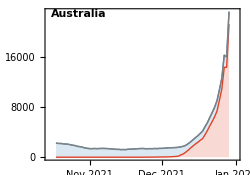
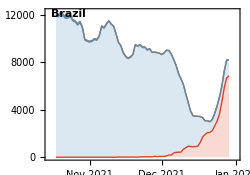
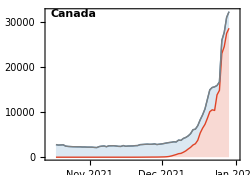
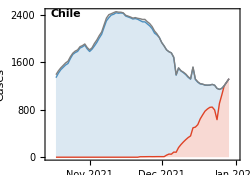
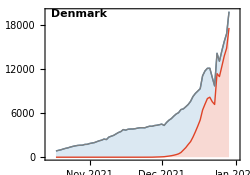
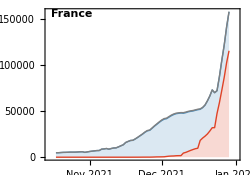
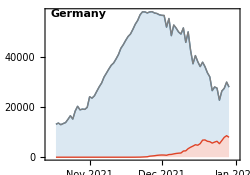
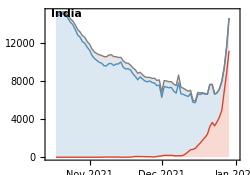
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png